-Graphics-

# Mathematica for Finance

## Introduction to the world’s leading technical computing platform

Igor Hlivka
Wolfram Training
igor.hlivka@zelof.co.uk

## Table of Contents

Introduction to Mathematica

Why Mathematica?

Mathematica basics

Mathematica programming

Declarations, assignments, functions

Symbolic programming

Procedural programming

Lists

Functional programming

Symbolic and numerical operations with Mathematica

Algebraic operation

Solving equations

Calculus

Differential equations & partial differential equations

Optimisation

Probability and statistics

Descriptive statistics

Probabilities

Finance applications with Mathematica

Random processes

SDE processes

PDE approach

Option pricing

Risk applications

Visualisation

Excel Link

## Introduction to Mathematica

What is Mathematica?

CAS for doing mathematics by computer

Wolfram Research - the leader in technical computing with innovative design, integrated approach and depth of coverage

The most comprehensive system for technical disciplines on the market with 5,000 functions and calls covering symbolic and numerical mathematics, algorithms, geometry, visualisation, imaging, data and interactive analysis

Modernly designed, robust and efficient - suitable for large-scale industrial applications with parallelisation, multi-threading paradigm and connectivity to almost everything (180 file formats, APIs, databases etc.)

### Core foundations of Mathematica

Wolfram Programming Language [WPL] and Notebook interface are central to the Mathematica foundation of the system. The  knowledge-based symbolic language and flexible document-based interface that let mixing executable code, richly formatted text, dynamic graphics, and interactive interfaces on a single page make Mathematica unique in its design, feel & look and the purpose.

## Wolfram Programming Language

Functional programming environment built on top on rule-based engine which operates on general symbolic trees. Mathematica primarily consists of:

Powerful rule-based engine with pattern-matching and evaluation built around Mathematica’s expression

==> This is the first principle:  everything is an expression

Global rule base which allows the user the define functions as rules and make them interact with the system’s pre-built rules in non-trivial way

==> This is the second principle: pattern-matching and rule substitution

Highly optimised and efficient structural operators on lists and arrays

==> This is the third principle: expression evaluation

Support of functional programming paradigm by the possibility to define pure functions and by efficient built-in higher-order functions. This can be applied to any expression

The power of symbolic programming - replication in other languages will require re-writing a substantial part of Mathematica

Many problems can be solved with Mathematica with much less effort and much faster  than in other programming languages because of many built-in generic and specific functions

Ideal tool for prototyping, modelling, simulation, validation pro gramme design and ideas testing

Multiparadigm language - the richness of the WPL allows to select for any problem a programming paradigm that suits it best. Thanks to its high level specification, you can spend most time on problems themselves rather than thinking on implementation

The first “problem-oriented” language - it allows choosing a programming style that is best suited for a given problem. It also supports one to program and research at the same time- the true power of modern mathematics

Ease and speed of writing and debugging the code. Extremely small size of the code and the ability to stay at high abstraction level when solving the problem

This allows single person to manage substantial projects

### Basic operations

Mathematica’s primary structure is Cell where we input all commands and textual inputs

In Mathematica everything is an expression

```mathematica
2*3+15
```

```mathematica
4+5^2-√13
```

Exact results can be efficiently turned into numerical equivalents (where appropriate)

```mathematica
%//N
```

```mathematica
300!
```

Expression can contain anything - eg. symbolic mathematical expression

```mathematica
3x+5y-3z
```

That can be modified further with precedence expression

```mathematica
%^3
```

```mathematica
%//Expand
```

Mathematical implications are carried out automatically

```mathematica
3x+7x
```

...but one has to be careful to preserve the mathematical logic

```mathematica
x3+x7
```

Mathematica treats this as two different variables => x_3 and x_7

#### Boolean operations

Mathematica supports the full range of boolean operations on expressions - including relational and logical tests

```mathematica
3>5
```

```mathematica
5≥5
```

```mathematica
3==3
```

```mathematica
(3>6)||(5>4)
```

```mathematica
(2>1)&&(3>4)
```

#### Operations precedence

Mathematica has rules which determine the relative precedence of all of its operators, meaning that it knows which should precede the others in evaluating pieces of an expression

Arithmetic operations have higher precedence than relational and logical
operations

```mathematica
4>2+3
```

Within the category of boolean operations, relational operations have
higher precedence than logical operations

```mathematica
5>4&&1>2&&3≥3
```

#### Exact and approximate values

In Mathematica, there are two important sorts of values, exact and
approximate. Exact values usually take more space to store and calculations with exact values require more time to insure an exact answer. Approximate values usually take less space to store and calculations with approximations require less time. 

Exact values may either be (a) integers or fractions or (b) symbolic names for constants such as E, Pi, and Sqrt[2], from which Mathematica knows how to find as many digits as necessary in any computation. Approximate values are most typically numeric expressions containing a decimal point.

If an expression contains only exact values, Mathematica will never approximate it and will instead leave the expression in a simple exact form

```mathematica
Pi
```

```mathematica
Sqrt[5]
```

```mathematica
3^25/6
```

The conversion between the exact and approximate values - function ‘N[]’

```mathematica
N[Pi]
```

```mathematica
N[Pi,50]
```

## Mathematica programming

#### Variable declarations and initialisation

```mathematica
a=7
```

```mathematica
y=2 a -a^2+3
```

```mathematica
?a
```

```mathematica
(a+y)^2
```

```mathematica
a+=2
```

```mathematica
y-=3x+5
```

```mathematica
a*=2x+1/2
```

```mathematica
f=Sin[1/x]Cos[x^2]/√x
```

De-assignment / Undeclaration

```mathematica
Clear[a]
```

```mathematica
a
```

```mathematica
{y,f}=.
```

We can also initialise indexed variables

```mathematica
{b[1]=9,b[3]=7,b[5]=10}
```

```mathematica
2b[1]-3b[2]+4b[3]/b[4]+6b[5]
```

```mathematica
Clear[a,b,c,x,y,z];
```

#### Immediate and Delayed assignment

There are two assignment commands in Mathematica: immediate and delayed

The immediate assignment (=), say x = y, which means “assign to x the value that y has right now”.  For delayed assignment, one has to use (:=) (semicolon plus an equal sign), say x:=y. This means “add to the global rule base a rule, which will substitute x every time that x is encountered, by the value that y will have at that moment”. So, with this kind of assignment, the right hand side is not evaluated at the moment of assignment, but is re-evaluated every time when the left-hand side appears somewhere in the program.

```mathematica
Clear[a,b];
a=Random[Integer,{1,15}];
Do[Print[a],{5}]
```

```mathematica
b:=Random[Integer,{1,15}];
Do[Print[b],{5}]
```

```mathematica
{a,b}=.
```

#### Set and SetDelayed : when which one is used

Normally we use Set (=) to define variables, and SetDelayed (:=)  to define functions, for which the recomputation of the r.h.s. on a changed argument is a natural operation. 

However, in this respect Mathematica differs from other programming environments in that the distinction between functions and variables is achieved not on the level of keywords such as <function>, or specific forms of functions declaration, but essentially by the assignment operator that have been used to define the symbol , and also to some extent by a type of global rule associated with the symbol.

So what? This allows to work with functions and variables on equal grounds. This lack of fundamental distinction between functions and variables is at the heart of the functional style of programming, which is one of the most efficient programming styles in Mathematica

#### Functions

Functions extend the expression assignment with rules, patterns and transformations

```mathematica
Clear[f];
f[x_]:=x^3
```

```mathematica
{f[2],f[3y],f[a],f[something]}
```

You can assign the function to a particular value

```mathematica
f[2]=7.5
```

```mathematica
{f[3/2],f[2],f[3]}
```

```mathematica
Clear[f];
f[x_Integer]:=x^3
```

```mathematica
{f[4],f[0.25],f[a]}
```

Functions with several variables

```mathematica
Clear[f];
f[x_,y_,z_]:=x+y-z^2
```

```mathematica
f[2,x,a]
```

Restrictions on the parameters - programming with constrains

```mathematica
Clear[g];
g[x_,y_]:=x-1/y/;x>y
```

```mathematica
{g[3,2],g[2,3]}
```

```mathematica
numRoot[x_]:=√N[x]/;x≥0
```

```mathematica
numRoot[-12]
```

```mathematica
sumRoot[x_,y_]:=√N[x+y]/;x+y≥0
```

```mathematica
{sumRoot[5,-2],sumRoot[-5,2]}
```

```mathematica
mypiecewise[x_]:=x/;x≥0
mypiecewise[x_]:=-x/;x<0
```

```mathematica
Plot[mypiecewise[x],{x,-3,3}]
```

#### Patterns & Symbolic programming

Pattern-matching is a feature found primarily in symbolic programming languages such as Mathematica, but not in procedural or object-oriented languages such as C, C++, or Java. The most basic sort of pattern matching is data type checking for parameters, followed by general boolean parameter tests (and their variants, conditions) and then more structured patterns, with which we can assign parameter names to parts of a parameter

```mathematica
Clear[f,a,b,c];
f[x_List]:=x^2
f[x_List,y_List]:=Join[x,y];
f[x_?NumberQ]:=x/3
f[x_?EvenQ]:=x^3/4
```

```mathematica
{f[2],f[4.2],f[{2,3,5}],f[{a,c},{3,5,8}]}
```

#### Replacements and transformations

```mathematica
expr=2+x+x^2+y^3+z^2+x^2 Sin[z]-Cos[x];
```

We can transform the expression with the set of transformation rules

```mathematica
expr/.x->a
```

```mathematica
expr/.Sin[x_]->Cosh[x^2+3x]
```

```mathematica
expr/.{y->√g[a,t],z->Log[2x]}
```

```mathematica
expr/.z->{a,b,c}
```

#### Rule and RuleDelayed transformations

```mathematica
testdata={2,a,3,5,1/4,b,a,d,a};
```

Rule-based transformation

```mathematica
testdata/.a->Random[]
```

RuleDelayed transformation

```mathematica
testdata/.a:>Random[]
```

Case when Rule will not be working......

```mathematica
n=1;
testdata/.a->{a,n++}
```

...but RuleDelayed will

```mathematica
testdata/.a:>{a,n++}
```

#### More on rules and transformations

```mathematica
testexp=Expand[(1+x)^10]
```

We can easily get the members as a list

```mathematica
testexp/.Plus->List
```

We want to replace even powers with α

```mathematica
testexp/.Plus->List/.x^(_?EvenQ)->α
```

Alternatively, we may want to assign some function <g> to these even powers

```mathematica
testexp/.x^(y_?EvenQ):>g[x^y]
```

Function g[x] can be anything....

```mathematica
%/.g[x_^y_]:>Sin[x-b]^y
```

#### Procedural programming

Procedural programming has a limited use in Mathematica as many traditional procedural routines (loops and iterators) can be accomplished with WPL more efficiently

Local variables

Module mechanism is the preferred route to define local variables in the code

```mathematica
rot2D[{x_,y_},φ_]:=Module[{sinφ=Sin[φ],cosφ=Cos[φ]},{{cosφ,-sinφ},{sinφ,cosφ}}.{x,y}]
```

```mathematica
rot2D[{1,1},Pi/4]
```

While loop

finding the first negative number in the list

```mathematica
firstNeg[x_List]:=Module[{i},i=1;
While[x[[i]]≥0,i++];
x[[i]]]
```

```mathematica
firstNeg[{3,5,2,-7,4,3,11,-2,0,-1,8}]
```

Fixed point iteration

```mathematica
myFixedPoint[f_,x0_]:=Module[{oldx,newx},oldx=x0;
newx=f[x0];
While[oldx≠newx,oldx=newx;
(*replaces oldx with last computed value*)newx=f[newx];
(*computes a new value*)];
newx  (*returns answer*)]
```

```mathematica
myFixedPoint[Cos,0.0]
```

Do loop

Finding the sum of squares of even numbers between the two numbers

```mathematica
sumEvSq[x_?EvenQ,y_?EvenQ]:=Module[{sum,i},sum=0;
Do[sum=sum+i^2,{i,x,y,2}];
sum]
```

```mathematica
sumEvSq[1000,2000]
```

Fibonacci numbers with the Do loop

```mathematica
Clear[fib];
fib[n_Integer?Positive]:=Module[{oldfib,newfib,newestfib},oldfib=1;
newfib=1;
newestfib=2;
Do[oldfib=newfib;
newfib=newestfib;
newestfib=oldfib+newfib,{n-3}];
If[n≤2,1,newestfib]]
```

```mathematica
fib[13]
```

For loop

For loop is a dedication to C programming and is not used frequently in Mathematica. It is also one of the least efficient ways to do the iterations.
Sum of Harmonic series up to given target

```mathematica
Clear[hrmSum]
hrmSum[goal_?NumberQ]:=Module[{sum,n},For[sum=0;n=1,sum≤goal,n++,sum+=1/n];
n-1]
```

```mathematica
hrmSum[2]
```

Fibonacci numbers re-visited with the For loop

```mathematica
Clear[fib];
fib[n_Integer?Positive]:=Module[{oldfib,newfib,newestfib,i},For[oldfib=newfib=newestfib=i=1,i≤n-2,i++,oldfib=newfib;
newfib=newestfib;
newestfib=oldfib+newfib];
newestfib]
```

```mathematica
fib/@Range[20]
```

### Lists

Lists are the main data structure in Mathematica. Any complex data structure can be represented as some complex and nested list. For example, N-dimensional array is represented as a list with depth N. Any tree can also be represented as a list.

Lists can be generated dynamically during the process of program execution, and the correctly written functions work on lists of arbitrary length without taking the length of the list as an explicit parameter. This results in a quite “clean” code, which is at the same time easy to write. 
Another advantage of lists is that it is usually easy to debug functions that work on them 

Lists are not required to contain only elements of the same type - they can contain any Mathematica expressions mixed in an arbitrary way. These expressions may themselves be lists or more general Mathematica expressions, of any size and depth.

#### Functional generation of lists in Mathematica

Range function

Suitable for list generation with equidistant numbers

```mathematica
Range[5]
Range[4,15]
Range[0,1,0.1]
```

Table function

When we need lists of more general nature, often they can be generated by the Table command:

```mathematica
Table[i^2,{i,1,10}]
Table[i*j,{i,1,3},{j,1,3}]
Table[i+j+k,{i,1,2},{j,1,3},{k,1,3}]
```

Matrices can be easily built with the Table command

```mathematica
Clear[i,j,x]
Table[x^(i+j),{i,1,3},{j,1,3}]
```

```mathematica
%//MatrixForm
```

Avoid procedural paradigms when building lists

Loops are the least efficient processes in Mathematica

Example - the list of Sin[] values

Loop structure

```mathematica
For[testlist={};i=1,i≤10,i++,testlist=Append[testlist,Sin[i]]];
testlist
```

Mathematica solution

```mathematica
Sin[Range[10]]
```

#### Working with lists

```mathematica
Clear[mylist]
myList=Range[1,27,3]
```

Part extraction

Want to extract 3rd element

```mathematica
myList[[3]]
```

Want 3rd, 6th,8th element

```mathematica
myList[[{3,6,8}]]
```

2nd from the end of the list

```mathematica
myList[[-2]]
```

Working with nested lists

```mathematica
nestlist=Range[5 #,5 #+3]&/@Range[4]
```

Extract 2nd sublist

```mathematica
nestlist[[2]]
```

Extract 1st and 3rd sublist

```mathematica
nestlist[[{1,3}]]
```

Taking 3rd element in the 2nd sublist

```mathematica
nestlist[[2,3]]
```

Taking several elements in one go

```mathematica
Take[myList,4]
Take[myList,{2,5}]
Take[myList,-2]
Take[nestlist,2]
Take[nestlist,All,2]
Take[nestlist,{2,4},{1,3}]
```

Dropping elements from the list

```mathematica
Drop[myList,2]
Drop[myList,{2,6,2}]
Drop[nestlist,{1,3,2}]
```

List length

```mathematica
Length[myList]
Length[nestlist]
Table[Length[nestlist[[i]]],{i,Length[nestlist]}]
```

List modification

```mathematica
myList[[3]]=a;
myList
```

```mathematica
nestlist[[All,3]]=b;
nestlist
```

```mathematica
nestlist[[All,2]]={a,b,c,d};
nestlist
```

Position in the list

```mathematica
Position[myList,4]
```

```mathematica
Position[nestlist,12]
```

More complex case

```mathematica
nestlist2=Range/@Range[6]
```

```mathematica
Position[nestlist2,3]
```

Get the position of all odd numbers

```mathematica
Position[nestlist2,_?OddQ]
```

Get the addresses of the same first element

```mathematica
Split[%,First[#1]==First[#2]&]
```

Adding elements to the list

```mathematica
Clear[myList];
myList=Range[1,27,3]
```

```mathematica
Append[myList,a]
```

```mathematica
Prepend[myList,b]
```

```mathematica
myList
```

#### Working with matrices

In Mathematica matrix is simply list of lists

```mathematica
myMatrix={{1,2,3},{a,b,c},{X,Y,Z}}
```

Expressing it in matrix form

```mathematica
myMatrix//MatrixForm
```

All operations we discussed on lists apply natively to matrices. Special operators on matrices:

```mathematica
Diagonal[myMatrix]
```

```mathematica
Reverse[myMatrix]//MatrixForm
```

```mathematica
{RotateLeft[myMatrix]//MatrixForm,RotateRight[myMatrix]//MatrixForm}
```

Transposing of matrix

```mathematica
Transpose[myMatrix]//MatrixForm
```

Inverting matrix

```mathematica
Inverse[myMatrix]//MatrixForm
```

Augment the matrix by row / column

```mathematica
Join[IdentityMatrix[3],{{a,b,c}}]//MatrixForm
```

```mathematica
Join[IdentityMatrix[3], Transpose[{{a,b,c}}],2]//MatrixForm
```

Flattening the matrix

```mathematica
Flatten[myMatrix]
```

Flattening down to a given level

```mathematica
Flatten[{{a,b},{c,{d},e},{f,{g,h}}},1]
```

Use of Flatten command: a computation of quadratic norm of a tensor of arbitrary rank (vector, matrix etc)

See how Flatten can dramatically simplify the computation of the norm of a tensor of arbitrary rank. What may be surprising is that we will not need the rank of the tensor as a separate parameter

```mathematica
Clear[tensorNorm];
tensorNorm[x_List]:=√(Plus@@Flatten[x^2])
```

```mathematica
testmat2=Table[i*j,{i,1,6},{j,1,6}]
```

```mathematica
tensorNorm[testmat2]
```

The function works well on a tensor of any rank without modifications! It would be hard to do this without Flatten, and in particular, in languages like C we would need nested loops to accomplish this

#### Pure functions

The notion of a pure function comes from the λ - calculus, and is widely used in functional programming languages, Mathematica in particular. 

From the practical viewpoint, we often need some intermediate functions which we have to use just once, and we don' t want to give them separate names. Pure functions allow to use them without assigning them names, storing them in the global rule base.

In Mathematica, the pure function can be defined in two ways: 
	a) through the built-in function <Function>
	b) through the so-called #-& notation

Function approach

```mathematica
Function[x,(x>10)&&(x<50)][4]
```

```mathematica
Function[x,(x>10)&&(x<50)] /@ {1,20,100,30}
```

```mathematica
Select[Table[i^2,{i,10}],Function[x,(x>10)&&(x<50)]]
```

#-& approach

We do not need the name x in the pure function either. We can replace it with # and write only the function definition

```mathematica
Select[Table[i^2,{i,10}],(#>10)&&(#<50)&]
```

We can also write definitions with pure functions

```mathematica
geometricMean=(#1 #2 #3)^(1/3)&;
```

```mathematica
geometricMean[a,b,c]
```

```mathematica
Intersection[#1,#2]&[{1,2,3,4},{3,4,5,6}]
```

As an example, consider a pure function which sorts its argument (list of lists is assumed), in an ascending order in the first elements of the sublists

```mathematica
Clear[sortFirst];
sortFirst=Sort[#1,First[#1]≤ First[#2]&]&;
```

```mathematica
sortFirst[{{2,3},{6,7},{3,11},{1,3},{5,1}}]
```

### Functional programming

Functional programming paradigm is the programming style in which the central role is played by application of functions, to both data and other functions. Functions themselves are treated as data, and thus can be arguments of other functions. Since any data structure can be represented as a list, functional programming is about application of functions to lists. 

Apart from being concise, the functional programming style is usually the most efficient in Mathematica. It is possible to use functional programming techniques on expressions more general than lists - basically, on any Mathematica expressions. This is a very powerful capability

Map function

This is one of the two most fundamental built-in higher order functions, and by far the most frequently used one

```mathematica
Clear[f]
f[x_]:=x^2
```

```mathematica
Map[f,{a,b,c}]
```

Elegant and efficient replacement for loops

```mathematica
Map[#^2&,{a,b,c}]
```

Using shorthand

```mathematica
f/@{a,b,c}
```

```mathematica
#^2&/@{a,b,c}
```

```mathematica
#^2&@f/@{a,b,c}
```

However

```mathematica
#^2&@(f/@{a,b,c})
```

```mathematica
First/@{{a,b},{c,d},{h,g},{k,l}}
```

Partial sums with Map function

```mathematica
partsum[x_List]:=Module[{sum=0},sum+=#&/@x]
```

```mathematica
partsum[Range[15]]
```

Using Map to sort sublists

```mathematica
Clear[testlist];
testlist=Table[RandomInteger[{1,10}],{3},{2},{4}]
```

```mathematica
Map[Sort,testlist,{2}]
```

in decreasing order

```mathematica
Map[Sort[#,GreaterEqual]&,testlist,{2}]
```

MapAt function

Similar to Map, but it maps the function to specific position(s) rather than on an entire list

```mathematica
Clear[myList];
myList={a,b,c,d}
```

We want to map Cos function to the 3rd element on the list

```mathematica
MapAt[Cos,myList,3]
```

If we want to map at 2nd and 3rd element

```mathematica
MapAt[Cos,myList,{{2},{3}}]
```

MapAt is frequently used with Map. Example - we may want to map Sine function to the 2nd element of each sublist

```mathematica
Clear[nestlist];
nestlist=Table[RandomInteger[{1,10}],{3},{2},{3}]
```

```mathematica
Map[MapAt[Sin,#,2]&,nestlist,{2}]
```

If we want to map the Log function to each even number in the list

```mathematica
MapAt[Log,nestlist,Position[nestlist,_?EvenQ]]
```

or mapping f function to all multiples of 3

```mathematica
MapAt[f,nestlist,Position[nestlist,x_/;Mod[x,3]==0]]
```

However, MapAt is known to be slower on very large lists when simultaneous mapping at particular sublist is required.

Apply function

Apply is the second "fundamental" higher-order function in the FP programming paradigm. Its action is different from that of Map or related functions. Apply takes a function <f> as its first argument, and an expression <expr>as a second one. It changes the head of <expr> from what it was to <f>

```mathematica
Clear[a,b,c];
Apply[List,a+b+c]
```

```mathematica
Apply[Plus,a b c]
```

Shorthand notation:  “@@”

```mathematica
Plus@@Range[10]
```

Conditional summing of even elements of the list - only if all elements are even

```mathematica
Clear[sumEven];
sumEven[x_List]/;And@@Map[EvenQ,x]:=Plus@@x;
```

```mathematica
sumEven[Range[0,10,2]]
```

```mathematica
sumEven[Range[10]]
```

Apply is frequently used in conjunction with Map: the shorthand “@@@”

Consider the following problem: we have a list of lists of numbers. The sublists have various length. We have to multiply all the numbers in each sublist.

```mathematica
Clear[myList];
myList=Table[RandomInteger[{1,10}],{10},{RandomInteger[{3,7}]}]
```

```mathematica
Times@@@myList
```

## Symbolic and numerical routines with Mathematica

### Algebra

```mathematica
12(3+x)(x+y)+(x+y)^2
```

```mathematica
Expand[%]
```

```mathematica
%^3
```

```mathematica
Expand[%]
```

```mathematica
CoefficientList[%,{x,y}]
```

```mathematica
Simplify[%%]
```

```mathematica
FullSimplify[%%%]
```

### Solving equations

```mathematica
eq1=a x^2+b x+c==0;
```

```mathematica
Solve[eq1,a]
```

```mathematica
Solve[eq1,x]
```

Substitute the result for the solved variable - say 1st result

```mathematica
x/.%[[1]]
```

```mathematica
Solve[a x^3+b x^2+c x+d==0,x]//Simplify
```

```mathematica
Solve[a x^4+b x^3+c x^2+d x+e==0,x]
```

```mathematica
Solve[∑_(i=0)^5 Subscript[a, i] x^i==0,x]
```

#### Solving equations numerically

```mathematica
NSolve[x^5+2 x^2+3x-1==0,x]
```

```mathematica
NSolve[{2x+y^2==2,5x-3 y+√z==3,x^2-y^2+z^2==0},{x,y,z}]
```

```mathematica
FindRoot[{3 Cos[x^2]==Log[y],Sinh[y^3]==Log[x]},{{x,0.1},{y,1}}]
```

```mathematica
FindRoot[{Exp[x^2-2x]==√y,y^2==Log[x]},{{x,1},{y,1}}]
```

```mathematica
Clear[A,λ];
A={{1,2,3},{5,4,6},{4,5,7}};
FindRoot[{A.x==λ x,x.x==1},{{x,RandomReal[1,3]},{λ,1}}]
```

```mathematica
FindRoot[{{{1,2},{3,4}}.x==θ x,x.x==1},{{x,{1,2}},{θ,1}}]
```

Solving Linear system:

```mathematica
Clear[m,b];
m={{2,1,2},{1,2,3},{1,4,9}};
b={{1,2},{3,4},{5,6}};
LinearSolve[m,b]
```

```mathematica
Clear[m,b,n];
n=1000;
m=Table[i*j,{i,RandomReal[1,n]},{j,RandomReal[1,n]}];
```

```mathematica
LinearSolve[m,√RandomReal[1,n]]
```

### Calculus

```mathematica
D[Sin[x^2]Cos[1/x],x]
```

Second derivative

```mathematica
D[Exp[-x^2] √(1/x)Cos[x^2],{x,2}]
```

Third derivative

```mathematica
D[Log[x]Sinh[x^2],{x,3}]
```

Total derivatives

```mathematica
Dt[2x^2+3y^2+(1/z^2)^2,x]
```

Derivative of unknown function <f>

```mathematica
Clear[f];
D[x f[x^2],x]
```

Integration

```mathematica
Integrate[x^2 Sin[x]^2 Cos[x],x]
```

```mathematica
Integrate[Exp[1-x^2],x]
```

```mathematica
Clear[f,n];
Integrate[(1-x^2)^n,x]
```

```mathematica
Integrate[1/(x^4-y^4),x,y]
```

```mathematica
Integrate[2 x^2 Exp[-y^2] Sin[x y],x,y]
```

```mathematica
Integrate[BesselK[0,x] BesselJ[0,x],{x,0,Infinity}]
```

```mathematica
NIntegrate[2 x^2 Exp[-y^2] Sin[x y],{x,0,Pi},{y,1,2}]
```

### Differential equations

Solving ODE symbolically

```mathematica
DSolve[y'[x]+2y[x]==1,y[x],x]
```

```mathematica
DSolve[y'[x]-x y[x]==1,y[x],x]
```

```mathematica
DSolve[y'[x]-x y[x]^3+y[x]==0,y[x],x]
```

Applying boundary-value problem

```mathematica
DSolve[{y'[x]==a y[x],y[0]==1},y[x],x]
```

```mathematica
DSolve[{y'[x]-2y[x]^2==x,y[0]==π},y[x],x]//FullSimplify
```

Solving higher-order DE

```mathematica
DSolve[y''[x]-Exp[x] y[x]==0,y[x],x]
```

```mathematica
DSolve[x^2 y''[x]+y[x]==0,y[x],x]
```

```mathematica
DSolve[y'''[x]+x y[x]==0,y[x],x]
```

#### Partial differential equations

We can solve certain PDE symbolically

```mathematica
Clear[f,y];
DSolve[3D[f[t,x],t]-1/2 x^2 D[f[t,x],x]==0 ,f[t,x],{t,x}]
```

```mathematica
DSolve[{2D[y[t,x],t]+7D[y[t,x],x]==3,y[0,x]==π},y[t,x],{t, x}]
```

```mathematica
DSolve[{3D[y[t,x],t]-1/4 D[y[t,x],{x,2}]==0,y[0,x]==Subscript[x, 0]},y[t,x],{t,x}]
```

If symbolic solution fails, we can employ numerical methods for PDE solution. Mathematica offers powerful and flexible numerical solvers

```mathematica
NDSolve[{D[y[t,x],t]-1/4 D[y[t,x],{x,2}]==0,y[0,x]==Sin[x]},y,{t,0,1},{x,3,10}]
```

```mathematica
Plot3D[Evaluate[y[t,x]/.%],{t,0,1},{x,3,10}]
```

```mathematica
y[0.25,4]/.%
```

### Optimisation routines with Mathematica

WPL contains  is full range of state-of-the-art local and global optimisation modules both numeric and symbolic, including constrained nonlinear optimization, interior point methods, and integer programming. The WPL symbolic architecture provides seamless access to industrial-strength system and model optimisation, efficiently handling million-variable linear programming and multithousand-variable nonlinear problems.

#### Constrained optimisation with Linear Programming

LinearProgramming is the main function for linear programming with the most flexibility for specifying the methods used, and is the most efficient for large-scale problems.

Minimise:	3x+2y
s.t.		-5x+2y=7
x+y≥26
x≥2,y≥5

```mathematica
LinearProgramming[{3,2},{{-5,2},{1,1}},{{7,0},{26,0}},{{2,Infinity},{5,Infinity}}]
```

Larger-scale problem:

```mathematica
m=SparseArray[RandomChoice[{0.1,0.9}->{1.25,2.25},{50,200}]];
xi=LinearProgramming[Range[200], m, Table[0,{50}],Method -> "InteriorPoint"]
```

Solve large LPs, in this case 300,000 variables and 50,000 constraints:

```mathematica
lp1=LinearProgramming[Range[3 10^5],SparseArray[{Band[{1,1}]->1.,Band[{1,2}]->2.},{5*10^4,3 10^5}],Range[5*10^4]];//Timing
```

The solution is obtained with less than 2 sec

Take the first 25 values

```mathematica
Take[lp1,50]
Clear[lp1];
```

#### Local optimisation

WPL provides two major routines for numerical local optimisation:
a) FindMinimum
b) FindMaximum
They are based on linear programming methods with non-linear interior point algorithms and use the second derivatives.

```mathematica
Clear[f,x,s];
f=2Log[x] √x Cos[x];
s=FindMinimum[f,{x,2}]
```

```mathematica
Show[Plot[f,{x,0,10}],Graphics[{Red,PointSize[Large],Point[{x/.Last[s],First[s]}]}]]
```

#### Finance application

Let’s take the annual returns on bonds and stocks

```mathematica
Clear[R,μ,Σ,X];
```

```mathematica
R={{0.942,1.02,1.056,1.175,1.002,0.982,0.978,0.947,1.003,1.465,0.985,1.159,1.366,1.309,0.925,1.086,1.212,1.054,1.193,1.079,1.217,0.889},{0.852,0.735,1.371,1.236,0.926,1.064,1.184,1.323,0.949,1.215,1.224,1.061,1.316,1.186,1.052,1.165,1.316,0.968,1.304,1.076,1.1,1.012}};
```

Compute mean and covariances from these returns

```mathematica
μ=Mean[Transpose@R]
Σ=Covariance[Transpose@R]
```

Define variable X

```mathematica
X=Map[Subscript[x,#]&,{"Bonds","Stocks"}]
```

Minimise the portfolio’s volatility subject to at least 10% annual return:

```mathematica
FindMinimum[{X.Σ.X,Total[X]==1&&μ.X≥1.10&&Apply[And,Thread[X≥{0,0}]]},X]
```

#### Application of suprfunctions

Most of the specific algorithms in the Wolfram Algorithmbase are accessed through superfunctions and meta - algorithms, which automatically determine the optimal algorithm to achieve a particular task

FindShortestTour is one of the superfunctions  that captures concepts rather than and translates it into elegant and quick solution required by the user:

Case: Traveling salesmen of Europe

```mathematica
europe=CountryData["Europe"];
```

Find the Longitude and centers

```mathematica
pos=CountryData[#,"CenterCoordinates"]&/@europe;
```

Compute the shortest path

```mathematica
FindShortestTour[pos];
```

Display it

```mathematica
GeoGraphics[{Thick,Red,GeoPath[pos[[Last[%]]]]}]
```

## Probability and statistics

Mathematica offers the widest range of probabilistic and statistical functions and routines in the CAS market. There is probably no scientific area that is not being covered by WPL in probabilistic / statistical space. The WPL uses symbolic distributions and processes as models for random variables or random stochastic processes. The models can be automatically computed from data or analytically constructed from a rich library of built-in distributions and processes.

Let’s bring in financial data - CAC 40 Index

```mathematica
Clear[data];
data=TimeSeries[FinancialData["^FCHI","January 1,2013"]]["Values"];
ListPlot[data]
```

### Descriptive statistics

Location measures:

Mean, Median, Mode, Geometric Mean, Harmonic Mean, Trimmed Mean

```mathematica
location=Through[{Mean, Median, Commonest[#,1][[1]]&, GeometricMean, HarmonicMean, TrimmedMean}[data]]
```

```mathematica
BarChart[location,ChartStyle->"Pastel",PlotLabel->"Various location measures of the data"]
```

Dispersion measures

Variance, Standard Deviation, Mean Deviation, Median Deviation, Quartile deviation, Interquartile Range

```mathematica
return=Differences[Log[data]] √260;
ListPlot[return]
```

```mathematica
dispersion = Through[{Variance,StandardDeviation,MeanDeviation,MedianDeviation,QuartileDeviation,InterquartileRange}[return]]
```

```mathematica
BarChart[dispersion,ChartStyle->"Rainbow",PlotLabel->"Various dispersion measures of the data"]
```

We can identify the Max and Min of the return

```mathematica
Through[{Max,Min}[return]]
```

and the range of the return distribution

```mathematica
Max[#]-Min[#]&[return]
```

Identifying outliers

```mathematica
posmin={Position[return,Min[return]][[1,1]],Min[return]};
posmax={Position[return,Max[return]][[1,1]],Max[return]};
ListPlot[return,PlotRange->All,Epilog->{{PointSize[Large],Red,Point[posmin],PointSize[Large],Green,Point[posmax]}}]
```

and Quantiles....

```mathematica
Table[Quantile[return,i],{i,{5/100,10/100,25/100,75/100,90/100,95/100}}];
BarChart[%,ChartStyle->"TemperatureMap",PlotLabel->"CAC 40 return quantiles"]
```

Shape measures

Skewness, Kurtosis, Quartile Skewness

```mathematica
Through[{Skewness,Kurtosis,QuartileSkewness}[return]]
```

The return shows both negative skewness and quartile skewness => this indicates that the median is closer to the upper quartile

Return distribution

We employ histograms to get the distributional patterns in the data

```mathematica
Histogram[return,ChartStyle->"Rainbow"]
```

Comparison to Normal distribution

```mathematica
Histogram[return,Automatic,"PDF",Epilog->First@Plot[PDF[NormalDistribution[Mean[return],StandardDeviation[return]],x],{x,-0.6,0.6},PlotStyle->Red]]
```

The return distribution is not normal - we see higher peakedness and fatter tails

Obtaining a smooth histogram

```mathematica
SmoothHistogram[return,PlotStyle->{Blue,Thick},Filling->Axis]
```

We can examine tails in greater detail:

```mathematica
SmoothHistogram[return,PlotRange->{{-0.7,-0.5},All},PlotLegends->{"Return"},PlotLabel->"Left tail of the distribution",Epilog->First@Plot[PDF[NormalDistribution[Mean[return],StandardDeviation[return]],x],{x,-0.7,-0.5},PlotStyle->Red]]
```

```mathematica
SmoothHistogram[return,PlotRange->{{0.5,0.7},All},PlotLegends->{"Return"},PlotLabel->"Right tail of the distribution",Epilog->First@Plot[PDF[NormalDistribution[Mean[return],StandardDeviation[return]],x],{x,0.5,0.7},PlotStyle->Magenta]]
```

We can also fit the empirical distribution to the data

```mathematica
ed=HistogramDistribution[return,Automatic];
```

```mathematica
DiscretePlot[#[ed,x],{x,-0.6,0.6,0.005},PlotLabel->#]&/@{PDF,CDF}
```

```mathematica
pnts={0.25,0.3,0.35,0.4,0.45,0.5,0.6};
Table[Probability[x>i,x\[Distributed]ed],{i,pnts}];
BarChart[%,BarOrigin->Left,ChartElementFunction->"GlassRectangle",ChartLabels->pnts,ChartStyle->"DarkRainbow",PlotLabel->"Probabilities of exceeding certain thresholds"]
```

## Financial Applications with Mathematica

Mathematica provides finance-oriented platform combining powerful features of the core system and ever rising needs of the industry to cover new procedures, rules or market standards

It represents the ultimate response to the commanding trends of the sector - “fast, smart, integrated”

Algorithmic agility utilising modern, smart computation from other fields and injects refined computation into finance workflows—increasing your competitiveness in areas as diverse as option pricing, risk analysis, enterprise system development, and interactive reporting

### Random processes

Mathematica provides extensive range of random processes that can be applied in mathematical finance or any other scientific fields where randomness has to be analysed.
Random processes in Mathematica benefit from strong WPL foundation in probability theory and offer systematic coverage of random events with both symbolic and numerical support. Process simulation, parameters estimation, statistical computation and visualisation all come as standard

#### Library of available random processes in Mathematica

```mathematica
Grid[{{Item["", Frame -> {{False, True}, {True, False}},Background->None], "Discrete State", 
    "Continuous State"}, {"Discrete Time", 
    Column[{"BernoulliProcess", "BinomialProcess", "RandomWalkProcess", 
      "DiscreteMarkovProcess", "CompoundPoissonProcess", 
      "CompoundRenewalProcess"}, ItemSize -> {Automatic, Automatic}], 
    Column[{"MAProcess", "ARProcess", "ARMAProcess", "ARIMAProcess", 
      "SARMAProcess", "SARIMAProcess", "FARIMAProcess", 
      "CompoundRenewalProcess"}, ItemSize -> {Automatic, Automatic}]}, 
   {"Continuous Time", Column[{"PoissonProcess", "TelegraphProcess", 
      "ContinuousMarkovProcess", "QueueingProcess", "QueueingNetworkProcess", 
      "RenewalProcess", "CompoundPoissonProcess", "CompoundRenewalProcess"}, 
     ItemSize -> {Automatic, Automatic}], 
    Column[{"WienerProcess", "GeometricBrownianMotionProcess", 
      "BrownianBridgeProcess", "OrnsteinUhlenbeckProcess", 
      "CoxIngersollRossProcess", "FractionalBrownianMotionProcess", 
      "ItoProcess", "StratonovichProcess", "RenewalProcess", 
      "CompoundRenewalProcess"}, ItemSize -> {Automatic, Automatic}]}}, 
  Frame -> All, ItemSize -> {Automatic, Automatic}, ItemStyle -> "Text", 
  Spacings -> {1, 1},Background->White]
```

| Discrete State | Continuous State
Discrete Time | BernoulliProcess
BinomialProcess
RandomWalkProcess
DiscreteMarkovProcess
CompoundPoissonProcess
CompoundRenewalProcess | MAProcess
ARProcess
ARMAProcess
ARIMAProcess
SARMAProcess
SARIMAProcess
FARIMAProcess
CompoundRenewalProcess
Continuous Time | PoissonProcess
TelegraphProcess
ContinuousMarkovProcess
QueueingProcess
QueueingNetworkProcess
RenewalProcess
CompoundPoissonProcess
CompoundRenewalProcess | WienerProcess
GeometricBrownianMotionProcess
BrownianBridgeProcess
OrnsteinUhlenbeckProcess
CoxIngersollRossProcess
FractionalBrownianMotionProcess
ItoProcess
StratonovichProcess
RenewalProcess
CompoundRenewalProcess

### Time Series processes

We will explore the use of Time Series processes for data forecasting
Consider the USD-JPY exchange rate

```mathematica
Clear[jpy,mfit,fcast];
jpy=TimeSeries[FinancialData["JPY=X","January 5, 2014"]]
```

```mathematica
DateListPlot[jpy,Filling->Axis]
```

Alternative source

We fit the ARIMA model to the data

```mathematica
mfit=TimeSeriesModelFit[jpy,{"ARIMA",{60,1,0}}]//Quiet
```

Display the fitted model

```mathematica
mfit["BestFit"]
```

Forecast the exchange rate evolution over the next 30 days

```mathematica
fcast=TimeSeriesForecast[mfit,{30}];
DateListPlot[{jpy,fcast},Filling->Axis]
```

We can also simulate the data based on the fitted model

Projection for the next 90 days

```mathematica
mfitsim=RandomFunction[mfit,{90},25];
DateListPlot[{mfit["TemporalData"],mfitsim}]
```

How accurate is our forecast?

```mathematica
meanest=TimeSeriesThread[Mean,mfitsim];
ub=TimeSeriesThread[Quantile[#,0.95]&,mfitsim];
lb=TimeSeriesThread[Quantile[#,0.05]&,mfitsim];
{DateListPlot[meanest,PlotStyle->Purple,PlotLabel->"Expected FX in the next 90 days",ImageSize->350,PlotTheme->"Business"],DateListPlot[{ub,lb},PlotLabel->"Upper and lower confidence levels",PlotTheme->"Business",ImageSize->350]}
```

### SDE Processes

Mathematica has a number of defined SDE processes required in finance. These include: (i) Brownian motion, (ii) Geometric Brownian Motion, (iii) Ornstein-Uhlenbeck process, (iv) CIR process and (v) generic Ito / Stratonovich process. All processes are supported by symbolic and numerical schemes.

GBM process

```mathematica
Clear[gbm,t,μ,σ,x0,gbms];
gbm=GeometricBrownianMotionProcess[μ,σ,x0];
gbms=RandomFunction[gbm/.{μ->0.015,σ->0.25,x0->1},{0,2,0.01},1000];
ListLinePlot[gbms["Path",Range[25]]]
```

Price a MC 6M call and put option with strike K=1.15 when S_0=1 and the stock follows the GBM defined above

```mathematica
Clear[r,τ,call,put,k];
r=0.013;
τ=0.5;
k=1.15;
call=Exp[-r τ] NExpectation[Max[x[τ]-k,0],x\[Distributed]gbms]
put=Exp[-r τ] NExpectation[Max[k-x[τ],0],x\[Distributed]gbms]
Clear[r,τ,call,put,k];
```

Jump-Diffusion process

Jump-diffusion process is a combined SDE process where the underlying variable is further affected by additional noise factor and occasionally jumps. The underlying process can be generally any SDE process whilst jumps are generally modelled by Poisson or Compound Poisson process

```mathematica
Clear[jProc,dProc,jdProc,jsim,dsim,jdsim];
jProc=PoissonProcess[0.75];
dProc=GeometricBrownianMotionProcess[0.015,0.2,1];
jdProc=TransformedProcess[w[t]+j[t],{w\[Distributed]dProc,j\[Distributed]jProc},t];
trun={0,1,0.05};
jsim=RandomFunction[jProc,trun];
dsim=RandomFunction[dProc,trun];
jdsim=RandomFunction[jdProc,trun];
```

```mathematica
{ListLinePlot[jsim,PlotLabel->"Jumps",PlotStyle->Black,ImageSize->250],ListLinePlot[dsim,PlotLabel->"Stoch process",PlotStyle->Red,ImageSize->250],ListLinePlot[jdsim,PlotLabel->"Jump-diffusion",PlotStyle->Magenta,ImageSize->250]}
```

Let’s apply the Compound Poisson process to the GBM to create Merton Jump-Diffusion process

```mathematica
gProc=GeometricBrownianMotionProcess[0.015,0.2,1];
jdMerton=TransformedProcess[x[t]+y[t],{x\[Distributed]gProc,y\[Distributed]CompoundPoissonProcess[0.075,NormalDistribution[0.075,0.15]]},t];
```

Simulate the process

```mathematica
jdMsim=RandomFunction[jdMerton,{0,1,0.01},1000];
ListLinePlot[jdMsim["Path",Range[15]]]
```

Although the presence of jumps is not immediately visible, we can take some statistics from the distribution to see the impact

```mathematica
dMean=Table[{i,Mean[gProc[i]]},{i,0,1,0.05}];
jdMean=Table[{i,Mean[jdMsim[i]]},{i,0,1,0.05}];
ListLinePlot[{dMean,jdMean},PlotLegends->{"GBM mean","JD mean"},PlotStyle->{Blue,Red}]
```

```mathematica
dVol=Table[{i,StandardDeviation[gProc[i]]},{i,0,1,0.05}];
jdVol=Table[{i,StandardDeviation[jdMsim[i]]},{i,0,1,0.05}];
ListLinePlot[{dVol,jdVol},PlotLegends->{"GBM vol","JD vol"},PlotStyle->{Black,Magenta}]
```

We see higher mean and volatility due to the jumps

Let’s compare option prices

```mathematica
r=0.013;
τ=0.5;
k=1.15;
{Exp[-r τ] NExpectation[Max[x[τ]-k,0],x\[Distributed]gProc],Exp[-r τ] NExpectation[Max[x[τ]-k,0],x\[Distributed]jdMsim]}
```

As expected, the call option price is higher under the JD Merton model

```mathematica
Clear[gbm,gbms,jProc,dProc,jdProc,jsim,dsim,jdsim,gProc,jdMerton,jdMsim,dMean,jdMean,dVol,jdVol,r,τ,k,t,x];
```

#### Ito Process

Ito Process is a handy generic SDE wrapper that can be used to build bespoke or standartised SDE processes. It can be entered both in functional and differential form.

Example of Ito Processes:

```mathematica
ItoProcess[ⅆx[t]==(2θ-x[t])ⅆt+√(x[t](1-x[t]))ⅆw[t],x[t],{x,Subscript[x, 0]},t,w\[Distributed]WienerProcess[]]
```

```mathematica
ItoProcess[{μ,σ,Exp[x[t]]},{x,Subscript[x, 0]},t]
```

Bi-variate Ito Process

```mathematica
ItoProcess[{ⅆx[t]==-2y[t]ⅆt+ⅆw1[t],ⅆy[t]==-1/2 x[t]ⅆt+ⅆw2[t]},{x[t],y[t]},{{x,y},{0,0}},t,{Subscript[w, 1]\[Distributed]WienerProcess[],Subscript[w, 2]\[Distributed]WienerProcess[]}]
```

We can work with Ito Processes symbolically or numerically

```mathematica
{Mean[%[t]]//Simplify,Variance[%[t]]//Simplify}
```

Heston SDE process

Heston model is the classic stochastic volatility model used to price equity and fx options

```mathematica
cW[ρ_]:=ItoProcess[{{0,0},IdentityMatrix[2]},{{w1,w2},{0,0}},t,{{1,ρ},{ρ,1}}];
heston=ItoProcess[{
ⅆs[t]==μ s[t]ⅆt+√Abs[v[t]] s[t]ⅆSubscript[w, s][t],
ⅆv[t]==κ (θ-v[t])ⅆt+ξ √Abs[v[t]] ⅆSubscript[w, ν][t]},
{s[t],v[t]},{{s,v},{Subscript[s, 0],Subscript[v, 0]}},t,{Subscript[w, s],Subscript[w, ν]}\[Distributed]cW[ρ]];
```

```mathematica
hSim=RandomFunction[heston/.{μ->0.03,κ->0.01,θ->0.15,ξ->0.125,ρ->0.13,Subscript[s, 0]->10,Subscript[v, 0]->0.12},{0,1,0.01},3000,Method->"StochasticRungeKutta"] ;
{ListLinePlot[hSim["PathComponent",1]["Path",Range[20]],ImageSize->325,PlotLabel->"Price of the asset"],ListLinePlot[hSim["PathComponent",2]["Path",Range[20]],ImageSize->325,PlotLabel->"Variance of the asset"]}
```

Pricing MC call and put option with Heston StochVol model is easy

```mathematica
r=0.013;
τ=0.5;
Subscript[k, c]=14;
Subscript[k, p]=10;
Exp[-r τ] NExpectation[Max[x[τ]-Subscript[k, c],0],x\[Distributed]hSim["PathComponent",1]]
Exp[-r τ] NExpectation[Max[Subscript[k, p]-x[τ],0],x\[Distributed]hSim["PathComponent",1]]
```

```mathematica
Clear[cW,heston,hSim,r,τ,k,Subscript[k, c],Subscript[k, p],x,t];
```

Multi-factor IR model

```mathematica
chenmodel[θ_,ζ_,β_,η_,{r0_,α0_,σ0_}]:=ItoProcess[{
ⅆr[t]==(θ-α[t])ⅆt+√r[t] σ[t]ⅆw[t],
ⅆα[t]==(ζ-α[t])ⅆt+√α[t] σ[t]ⅆw[t],
ⅆσ[t]==(β-σ[t])ⅆt+√σ[t] η ⅆw[t]
},r[t],{{r,α,σ},{r0,α0,σ0}},t,w\[Distributed]WienerProcess[]
];
```

We can visualise the process paths

```mathematica
ListLinePlot[RandomFunction[chenmodel[0.028,0.03,0.01,0.02,{0.025,0.025,0.01}],{0,1,0.01},10,Method->{"StochasticRungeKutta","ProjectionFunction"->Function[{t,xvec},Abs[xvec]]}]]
```

Based on the model, we can define the price for zero-coupon bond

```mathematica
zcb[θ_,ζ_,β_,η_,{r0_,α0_,σ0_}]=ItoProcess[ⅆx[t]==r[t]ⅆt,Exp[-x[t]],{x,0},t,r\[Distributed]chenmodel[θ,ζ,β,η,{r0,α0,σ0}]];
```

```mathematica
rf=RandomFunction[zcb[0.04,0.07,0.05,0.1,{0.07,0.09,0.07}],{0,1,0.02},250,Method->{"StochasticRungeKutta","ProjectionFunction"->Function[{t,xvec},Abs[xvec]]}];
Plot[Mean[rf[t]]//Evaluate,{t,0,1},PlotLabel->Row[{"P(0,1) ≃ ",Mean[rf[1]]}],PlotTheme->"Marketing"]
```

```mathematica
Clear[chenmodel,r,α,σ,rf,zcb,t,xvec,td];
```

### PDE approach

Mathematica can solve certain PDE symbolically, however in most cases numerical solution is quicker and offers various refinements

Solution for the zero-coupon bond under the Vasicek short-rate model

```mathematica
Clear[κ,λ,μ,σ,T,drift,vol,pdesol];
drift=κ(μ-x)-λ*σ;
vol=σ;
{κ,λ,μ,σ,T}={0.015,0.0075,0.016,0.0075,1};
pdesol=NDSolve[{D[y[t,x],t]+drift* D[y[t,x],x]+1/2 vol^2*D[y[t,x],{x,2}]-x *y[t,x]==0,y[T,x]==1},y,{t,T,0},{x,0.01,0.2},InterpolationOrder->All]//Quiet
```

{{y→InterpolatingFunction[{{0., 1.}, {0.01, 0.2}}, <>]}}

```mathematica
Plot3D[Evaluate[y[t,x]/.pdesol],{t,0,1},{x,0.01,0.1},ColorFunction->Function[{x,y,z},Hue[z]]]
y[0,0.025]/.pdesol
```

-Graphics3D-

{0.975412}

```mathematica
Clear[κ,λ,μ,σ,T,drift,vol,pdesol];
```

Numerical PDE solution of the call option following CIR square-root diffusion process

```mathematica
Clear[κ,λ,μ,σ,T,drift,vol,k,pdesol2];
drift=κ(μ-x)-λ*σ;
vol=σ √x;
{κ,λ,μ,σ,T,k}={0.015,0.0075,0.016,0.1,1,0.025};
pdesol2=NDSolve[{D[y[t,x],t]+drift* D[y[t,x],x]+1/2 vol^2*D[y[t,x],{x,2}]-x *y[t,x]==0,y[T,x]==Max[0,x-k]},y,{t,T,0},{x,0.01,0.2},InterpolationOrder->All]//Quiet
```

{{y→InterpolatingFunction[{{0., 1.}, {0.01, 0.2}}, <>]}}

```mathematica
Plot3D[Evaluate[y[t,x]/.pdesol2],{t,0,1},{x,0.01,0.05},ColorFunction->"Rainbow"]
y[0,0.025]/.pdesol2
```

-Graphics3D-

{0.0054215}

```mathematica
Clear[κ,λ,μ,σ,T,drift,vol,k,pdesol2];
```

PDE for the stochastic volatility - Heston model

```mathematica
Clear[κ,λ,T,r,ρ,θ,k,ν,ω,pdesol5];
{κ,ω,r,θ,T,k,ρ,λ}={0.012,0.15,0.02,√0.2,1,1,-0.25,0.015};
pdesol5=NDSolve[{D[y[t,x,ν],t]+1/2 ν x^2*D[y[t,x,ν],{x,2}]+(r-1/2 ν)x D[y[t,x,ν],x]+ρ ν ω x D[y[t,x,ν],x,ν]+ 1/2 ω^2 ν D[y[t,x,ν],{ν,2}] - r y[t,x,ν]+(κ(θ-ν)-λ) D[y[t,x,v],ν] ==0,y[T,x,ν]==Max[0,x-k]},y,{t,T,0},{x,0.5,3},{ν,√0.1,√0.3},InterpolationOrder->All]//Quiet
```

{{y→InterpolatingFunction[{{0., 1.}, {0.5, 3.}, {0.316228, 0.547723}}, <>]}}

```mathematica
Plot3D[Evaluate[y[t,x,√0.17]/.pdesol5],{t,0,1},{x,0.5,2},ColorFunction->Hue]
```

-Graphics3D-

## Financial modelling

Mathematica natively supports a number of option payoofs in vanilla and exotic space. Both European and American option are available in the financial catalogue:

```mathematica
allDivs=FinancialDerivative[];
americanPoses=Flatten@Position[allDivs,{___,"American",___}];
americanOps=allDivs[[americanPoses]];
americOthers=First/@DeleteCases[americanOps,{__,"Call"|"Put"}];
americCalls=First/@Cases[americanOps,{__,"Call"}];
ameriPuts=First/@Cases[americanOps,{__,"Put"}];
europeanPoses=Flatten@Position[allDivs,{___,"European",___}];
europOps=allDivs[[europeanPoses]];
euroOthers=First/@DeleteCases[europOps,{__,"Call"|"Put"}];
euroCalls=First/@Cases[europOps,{__,"Call"}];
euroPuts=First/@Cases[europOps,{__,"Call"}];
others=DeleteCases[allDivs,{___,"European"|"American",___}|{_,_}];
MenuView[{Style["American Options","Text"]->MenuView[{Style["American Calls and Puts","Text"]->Grid[Partition[americCalls,5,5,1,""],Frame->All,ItemStyle->{"Text",Directive[FontSize->16]},Spacings->{1,1}],Style["American Others","Text"]->Grid[Partition[americOthers,3,3,1,""],Frame->All,ItemStyle->"Text",Spacings->{1,1}]},Alignment->Center,ImageSize->Automatic],
Style["European Options","Text"]->MenuView[{Style["European Calls and Puts","Text"]->Grid[Partition[euroCalls,5,5,1,""],Frame->All,ItemStyle->{"Text",Directive[FontSize->13]},Spacings->{1,1}],Style["European Others","Text"]->Grid[Partition[euroOthers,4,4,1,""],Frame->All,ItemStyle->"Text",Spacings->{1,1}]},Alignment->Center,ImageSize->Automatic],
Style["PerpetualLookback Options","Text"]->Grid[{{"Perpetual Lookback Call","Perpetual Lookback Put"}},Frame->All,ItemStyle->"Text",Spacings->{1,1}],
Style["Other Options","Text"]->Grid[Partition[others,3,3,1,""],Frame->All,ItemStyle->"Text",Spacings->{1,1}]
},Alignment->Center,ImageSize->Automatic]
```

#### Examples

American Call

```mathematica
FinancialDerivative[{"American","Call"}, {"StrikePrice"->30.00, "Expiration"->1},  {"InterestRate"-> 0.01, "Volatility" -> 0.1, "CurrentPrice"-> 30, "Dividend"->0.05}]
```

Implied volatility

```mathematica
FinancialDerivative[{"American","Call"}, {"StrikePrice"->40.00, "Expiration"->1, "Value"->0.85},  {"InterestRate"-> 0.01,"CurrentPrice"-> 40, "Dividend"->0.05}, "ImpliedVolatility"]
```

Sensitivities of the Asian call

```mathematica
FinancialDerivative[{"AsianArithmetic","European","Call"},{"StrikePrice"->50,"Expiration"->1,"Inception"->-1,"AverageSoFar"->50}, {"InterestRate"-> 0.01, "Volatility" -> 0.2, "CurrentPrice"-> 50, "Dividend"->0.05},{"Value","Greeks"}]
```

American double barrier (knockout) call option

```mathematica
FinancialDerivative[{"DoubleBarrierKnockOut","American","Call"},{"StrikePrice"->35,"Expiration"->1,"Barriers"->{25,40}},{"CurrentPrice"->30,"Dividend"->0.0134,"Volatility"->0.25,"InterestRate"->0.012}]
```

Volatility function for the Perpetual Lookback Put

```mathematica
ListPlot[{#,FinancialDerivative[{"PerpetualLookback","Put"},{"Expiration"->1,"MaxSoFar"->50},{"CurrentPrice"->45,"Dividend"->0.04,"Volatility"->#,"InterestRate"->0.015},"CriticalValue"]}&/@Range[0.1, 0.5, 0.02], Filling->Axis,PlotStyle->Red]
```

#### Probabilistic approach to financial modelling

Mathematica offers the widest range of probabilistic and statistical functions and routines in the CAS market

There is probably no scientific area that is not being covered by WPL in probabilistic / statistical space. The WPL uses symbolic distributions and processes as models for random variables or random stochastic processes

The models can be automatically computed from data or analytically constructed from a rich library of built-in distributions and processes

Integrated environment streamlines development, analysis, documentation, and delivery of custom financial models

Powerful symbolic engines returns exact solutions for many problems

Traditional B/S option formula

```mathematica
Clear[gPrc,callopt,k,x,μ];
gPrc=GeometricBrownianMotionProcess[μ,σ,Subscript[x, 0]];
callopt=Refine[Expectation[If[x[t]>k,x[t]-k,0],x\[Distributed]gPrc],k>0]//Simplify
```

Vega of the call option paying x^2-k

```mathematica
D[Refine[Expectation[If[x[t]>k,x[t]^2-k,0],x\[Distributed]gPrc],k>0],σ]//Simplify
```

```mathematica
Plot[%/.{Subscript[x, 0]->1,μ->0.01,k->1,t->0.5},{σ,0.1,0.5},PlotStyle->Magenta,PlotLabel->"Vega of the power option"]
```

```mathematica
Clear[gPrc,callopt,k,x,μ];
```

Vast playfield for custom financial models

Put option on the rate following Normal mean-reverting process

```mathematica
mProc=OrnsteinUhlenbeckProcess[μ,σ,θ,Subscript[x, 0]];
{mn,vol}={Mean[mProc[t]],StandardDeviation[mProc[t]]};
Expectation[If[x<k,k-x,0],x\[Distributed]NormalDistribution[α,β]];
putopt=%/.{α->mn,β->vol}//Simplify
```

Gamma on the above option

```mathematica
D[putopt,{Subscript[x, 0],2}]//Simplify
```

```mathematica
Clear[mProc,mn,vol,x,t,putopt,α,β];
```

Call option on the Gamma distributed asset

```mathematica
Clear[gDist,mn,vol,copt,soln];
gDist=GammaDistribution[a,b];
{mn,vol}={Mean[gDist],StandardDeviation[gDist]};
copt=Refine[Expectation[If[x>k,x-k,0],x\[Distributed]gDist],k>0];
soln=Solve[{mn==Subscript[x, 0]+μ t,vol==σ √t},{a,b}]//Flatten; {a/.soln,b/.soln};
copt/.{a->%[[1]],b->%[[2]]}
```

```mathematica
Plot3D[%/.{Subscript[x, 0]->0.05,k->0.05,t->0.25},{μ,0.01,0.03},{σ,0.01,0.03},ColorFunction->"SolarColors"]
```

```mathematica
Clear[gDist,mn,vol,copt,soln];
```

## Handling missing data

Missing or incorrect data is a frequent phenomenon in the industry

It can cause serious problems if the time series are required for special calculations - VaR, capital, various charges

Mathematica offers remedy and provides solutions to address the mising data problem

Let’s create an example with absent data in the time series

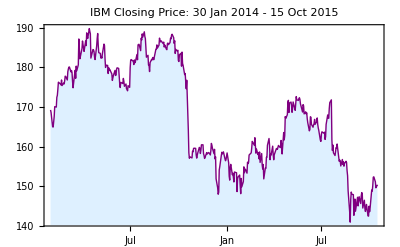

```mathematica
findata=TimeSeries[FinancialData["IBM",{2014,1,30}]];
DateListPlot[findata,PlotStyle->{Thick,Purple},FillingStyle->LightBlue,Filling->Axis,PlotLabel->"IBM Closing Price: 30 Jan 2014 - 15 Oct 2015"]
```

Remove part of the series to create the missing gap

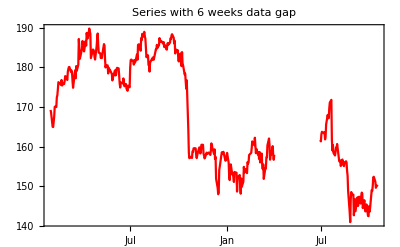

```mathematica
drange2=DateRange["April 6th,2015","June 26th,2015"];
mrange2=Table[{drange2[[i]],Missing[]},{i,Length[drange2]}];
finmis1=TimeSeriesInsert[findata,mrange2];
DateListPlot[finmis1, PlotLabel->"Series with 6 weeks data gap",PlotStyle->Red]
```

Mathematica offers built-in function for handling missing data

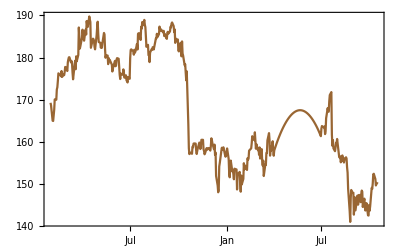

```mathematica
DateListPlot[TimeSeries[finmis1,
MissingDataMethod-> {"Interpolation",
InterpolationOrder->2},
ResamplingMethod->Automatic],PlotStyle->Brown]
```

We can do better with the Time Series models

Break the missing series into 3 components: (i) initial series, (ii) missing series, (iii) remaining series

```mathematica
inidata=TimeSeriesWindow[finmis1,{{2014,1,30},{2015,4,5}}];
resdata=TimeSeriesResample[inidata,ResamplingMethod->{"Interpolation",InterpolationOrder->1}];
lastdata=TimeSeriesResample[TimeSeriesWindow[finmis1,{{2015,6,22},{2015,10,15}}],ResamplingMethod->{"Interpolation",InterpolationOrder->1}];
```

We fit the long-tail AR model to the Time Series data

```mathematica
eproc=TimeSeriesModelFit[resdata,{"AR",20}]
```

TimeSeriesModel[…]

Calculate the length of the missing data window

```mathematica
pos=Flatten[Position[finmis1["Values"],_Missing]];
nmis=Length[pos]
```

82

Simulate the model for the missing period

```mathematica
eforecast=RandomFunction[eproc,{0,nmis}]
```

TemporalData[…]

Fill the gap with the simulated data

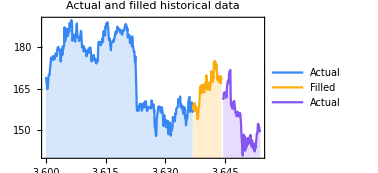
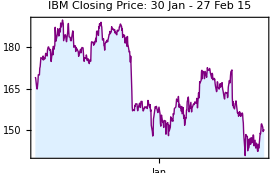

```mathematica
{DateListPlot[{resdata,eforecast,lastdata},Filling->Axis,PlotLabel->"Actual and filled historical data",PlotLegends->{"Actual","Filled","Actual"},ImageSize->280],DateListPlot[findata,PlotStyle->{Thick,Purple},FillingStyle->LightBlue,Filling->Axis,PlotLabel->"IBM Closing Price: 30 Jan - 27 Feb 15",ImageSize->280]}
```

## Risk

Mathematica supports rapid development and testing of robust financial risk models and deploying them as interactive applications or as high-performance infrastructure components—all from one system, with one integrated workflow.

Mathematica is unique in offering the reliability of a mixed symbolic-numeric approach to computation, multiple switching algorithms, built-in computable financial and economic data, and integrated parallel computation for scaling up performance

Novel approach and interactive visualisation allow simple, qualitative and comparative analysis to be done on the fly

```mathematica
port={"S1","S2","S3","S4","S5"};
mns={0.01,0.0145,0.002,-0.01,0.028};
vols={0.006,0.0069,0.01,0.012,0.0087};
corr=({{1, 0.2, 0.33, 0.1, 0.45}, {0.2, 1, 0.26, -0.12, -0.33}, {0.33, 0.26, 1, 0.3, -0.28}, {0.1, -0.12, 0.3, 1, 0.4}, {0.45, -0.33, -0.28, 0.4, 1}});
covar=Table[corr[[i,j]]*vols[[i]]*vols[[j]],{i,Length[vols]},{j,Length[vols]}];
mDist=MultinormalDistribution[mns,covar];
rets=Transpose[RandomVariate[mDist,300]];
```

```mathematica
TabView[
{Style["Histograms","Text"]->Module[{stockReturnTemp=rets[[All,All]],randomStocksTemp=port},
Row[Histogram[stockReturnTemp,Automatic,ChartStyle->"DarkRainbow",ChartLegends->randomStocksTemp,ImageSize->{500}]]],
Style["BoxWhiskerCharts","Text"]->Module[{stockReturnTemp=rets[[All,All]],randomStocksTemp=port},
Row[{ListAnimate[Table[BoxWhiskerChart[DeleteCases[stockReturnTemp,_Missing,Infinity],stl,ImageSize->Medium,PlotLabel->Style[stl<>" Box Whisker Chart","Text"],ChartElementFunction->"BoxWhisker",ChartLabels->port,ChartLegends->port,ChartStyle->"DarkRainbow",ImageSize->{450}],{stl,{"Basic","Median","Mean","Notched","Diamond","Outliers"}}],AnimationRunning->False]}]],
Style["DistributionCharts","Text"]->ListAnimate[Table[DistributionChart[DeleteCases[rets[[All,All]],_Missing,Infinity],PlotLabel->Style[elt,"Text"],ChartElementFunction->elt,ImageSize->Medium,ChartLabels->port,ChartLegends->port,ChartStyle->"DarkRainbow",ImageSize->{450}],{elt,ChartElementData["DistributionChart"]}],AnimationRunning->False]},Alignment->Center]
```

### Value at Risk

Value at risk and related risk measures area easily modelled and measured in Mathematica.  With more than 100 risk-related distributions, we can fit data to any model we desire

```mathematica
varcase=Join[RandomVariate[NormalDistribution[0.015,0.01],250],RandomVariate[LogisticDistribution[0.01,0.03],200],RandomVariate[StudentTDistribution[0.017,0.0175,2],275]];
ndfit=EstimatedDistribution[varcase,NormalDistribution[μ,σ]]
stdfit=EstimatedDistribution[varcase,StudentTDistribution[μ,σ,ν]]
jdfit=EstimatedDistribution[varcase,JohnsonDistribution["SU",α,β,μ,σ]]
```

```mathematica
Show[{Histogram[varcase,{.005},"PDF",PlotRange->{{-0.1,0.15},All}],Plot[{PDF[ndfit,x],PDF[stdfit,x],PDF[jdfit,x]},{x,-0.1,0.15},PlotRange->All,PlotStyle->{Black,Blue,Red},PlotLegends->{"ND","StdT", "Johnson"}]}]
```

Once the models have been fitted, we can easily get the VaR at a given confidence level. For example, @99% the risk static is:

```mathematica
clev=0.99;
ndvar=InverseSurvivalFunction[ndfit,clev];
stdvar=InverseSurvivalFunction[stdfit,clev];
jdvar=InverseSurvivalFunction[jdfit,clev];
Button[Style["Value at Risk Comparison","Text"],CellPrint[ExpressionCell[Grid[{{Style["Value at Risk\n Normal Distribution","Text",TextAlignment->Center],Style["Value at Risk\n StudentT Distribution","Text",TextAlignment->Center],Style["Value at Risk\n Johnson Distribution","Text",TextAlignment->Center]},
{Style[ndvar,"Text"],Style[stdvar,"Text"],Style[jdvar,"Text"]}},Frame->All,Spacings->{1,1}],"Text",ShowStringCharacters->False]]]
```

Getting Expected Shortfall (Tail Var) is straighforward:

```mathematica
ndES=NExpectation[x\[Conditioned]x<ndvar,x\[Distributed]ndfit];
stdES=NExpectation[x\[Conditioned]x<stdvar,x\[Distributed]stdfit];
jdES=NExpectation[x\[Conditioned]x<jdvar,x\[Distributed]jdfit];
```

```mathematica
Button[Style["Tail VaR Comparison","Text"],CellPrint[ExpressionCell[Grid[{{Style["Tail VaR\n Normal Distribution","Text",TextAlignment->Center],Style["Tail VaR\n StudentT Distribution","Text",TextAlignment->Center],Style["Tail VaR\n Johnson Distribution","Text",TextAlignment->Center]},
{Style[ndES,"Text"],Style[stdES,"Text"],Style[jdES,"Text"]}},Frame->All,Spacings->{1,1}],"Text",ShowStringCharacters->False]]]
```

### Extended risk modelling with highly cunstomised profile

Mathematica is perfectly suited to address arbitrary complexity in data and model definitions spanning beyond standard approach

Applying non-standard distributions to financial data provides additional level of risk assessments and leads to an elegant stress scenario testing
Example: Johnson distribution as the parametric risk density
This is the family of distributions where  X~NormalDistribution[0,1]] and Y=σ g((X-γ)/δ)+μ . 
We select one particular case of “unbounded” type where g(x)=sinh(x)

```mathematica
Manipulate[Column[{"JohnsonDistribution["<>ToString[α]<>","<>ToString[β]<>","<>ToString[μ]<>","<>ToString[σ]<>"]", Pane[Plot[Evaluate[PDF[JohnsonDistribution["SU",α,β,μ,σ],x]],{x,-0.2,0.2},Filling->Axis,FillingStyle->LightGray,PlotStyle->{Thick, Red},PlotRange->All],{700}]},Frame->All,Alignment->Center,ItemSize->Full],
{{α,0.7,"Alpha"},-2,2},{{β,0.3,"Beta"},0.01,2},{{μ,0.02,"Mu"},0.01,0.1},{{σ,0.03,"Sigma"},0.01,0.08},ControlPlacement->Left]
```

### VaR and CVaR with mixture distributions

We look at Normal - Rayleigh distribution mixture model where Rayleigh ‘part’ models the unknown value of the normal standard deviation. This type of mixture is a popular choice for risk parametrisation with non-normal dynamics

```mathematica
pmdist=ParameterMixtureDistribution[NormalDistribution[μ,σ],σ\[Distributed]RayleighDistribution[λ]];
```

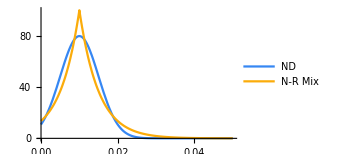
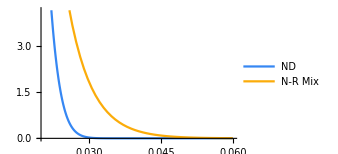

```mathematica
{Plot[{PDF[NormalDistribution[0.01,0.005],x],PDF[pmdist/.{μ->0.01,λ->0.005},x]},{x,0,0.05},PlotLegends->{"ND","N-R Mix"},ImageSize->250],Plot[{PDF[NormalDistribution[0.01,0.005],x],PDF[pmdist/.{μ->0.01,λ->0.005},x]},{x,0.02,0.06},PlotLegends->{"ND","N-R Mix"},ImageSize->250]}
```

Mixture distribution turns Normal density into semi-heavy tailed, however with good analytical tractability.
VaR and CVaR results are surprisingly simple.

```mathematica
pmVaR=Refine[InverseCDF[pmdist,α],1/2<α<1]//Simplify
```

```mathematica
pmCVaR=Refine[Expectation[x\[Conditioned]x>pmVaR,x\[Distributed]pmdist],λ>0&&1/2<α<1]//Simplify
```

```mathematica
Plot[{pmVaR/.{μ->0.01,λ->0.005},pmCVaR/.{μ->0.01,λ->0.005}},{α,0.5,1},PlotTheme->"Web",PlotLegends->{"VaR","CVaR"}]
```

Expected shortfall is materially higher than VaR as it captures distributional behaviour in the entire tail.

## Data Visualisation

Mathematica provides wide range of visaalisation options to display the data in desire ad format

Stochastic GBM process in 3D:

```mathematica
proc=GeometricBrownianMotionProcess[1,.2,.3];
sample=Table[RandomFunction[proc,{0,1,0.01},3]["ValueList"]ᵀ,{6}];
Graphics3D@Table[{ColorData["SolarColors"][RandomReal[]],Tube@Line@sample⟦i⟧},{i,6}]
```

-Graphics3D-

Combined charting of stochastic process

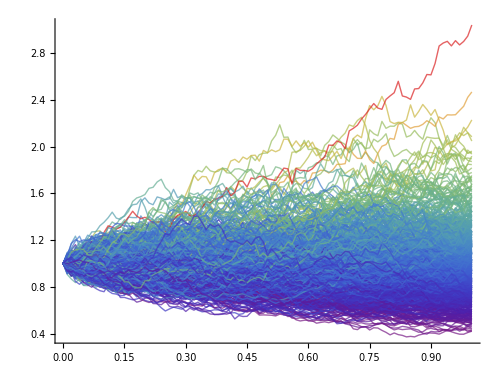

```mathematica
data=RandomFunction[GeometricBrownianMotionProcess[0,.3,1],{0,1,.01},750];
sd=data["SliceData",1];
cf=ColorData["Rainbow"];
sliced=BarChart[Last[#],Axes->None,BarOrigin->Left,AspectRatio->4,ChartStyle->(cf/@Rescale[MovingAverage[First[#],2],{Min[sd],Max[sd]},{0,1.5}]),ImageSize->85]&[HistogramList[sd,{Range[Min[sd],Max[sd],(Max[sd]-Min[sd])/25]}]];
ListLinePlot[data,ImageSize->500,PlotRange->All,
AspectRatio->3/4,Epilog->Inset[sliced,{1.01,0},{0,-1.17Exp@Mean[sd]}],PlotStyle->(cf/@Rescale[sd]),BaseStyle->Directive[Thin,Opacity[0.7]],PlotRangePadding->{{0,.2},{.5,.5}}]
```

Colored correlation matrix

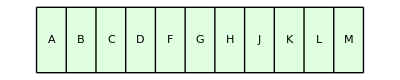
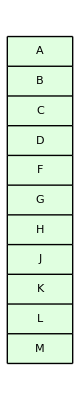
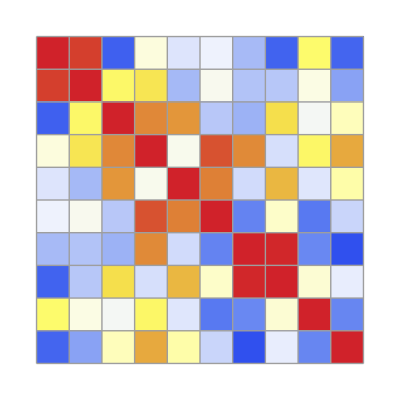
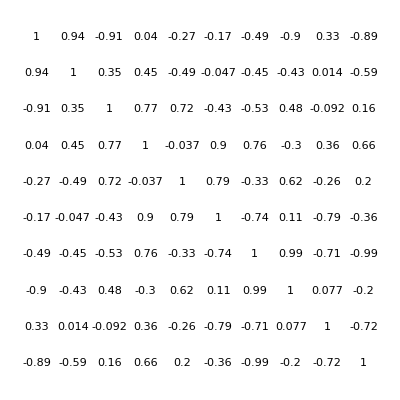

```mathematica
CM[n_]:=Module[{tb,ms},tb=Table[If[i==j,1/2,If[j>i,RandomReal[{-1,1}],0]],{i,n},{j,n}];
ms=tb+Transpose[tb]]
lab={A,B,C,D,F,G,H,J,K,L,M};
corr=CM[10];
s=300;
Column[{GraphicsRow[lab,ImageSize->{s},Background->LightGreen,Frame->All],Row[{GraphicsColumn[lab,ImageSize->{s},Background->LightGreen,Frame->All],Overlay[{ArrayPlot[corr,ColorFunction->(ColorData["TemperatureMap"][(1+#)/2]&),Frame->None,Mesh->True,PlotRangePadding->0,ImageSize->{s},ColorFunctionScaling->False],GraphicsGrid[Map[NumberForm[#,2]&,corr,{2}],BaseStyle->{FontSize->8},ImageSize->{s}]}]}]},Alignment->Right,Spacings->0]
```

Visualising moving averages

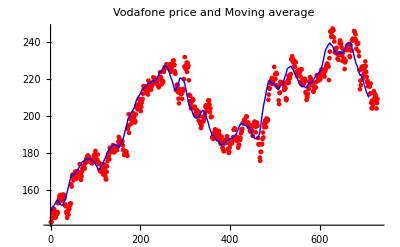

```mathematica
vod=FinancialData["VOD.L","Price",{2013,1,2},"Value"];
Show[ListPlot[vod,PlotStyle-> {Small,Red},PlotLabel->Style["Vodafone price and Moving average",17],PlotRange->Automatic],ListLinePlot[MovingAverage[vod,20],PlotStyle->{Thick,Blue}]]
```

## Excel Link for Mathematica

Excel Link for Mathematica facilitates the tow-way connectivity between Excel and Mathematica. The library of specially designed functions allow the user to read and write data to Excel ranges, display graphics, running Mathematica functions and routines in Excel and convert Mathematica expressions into Excel macros

Financial application in Excel running Mathematica

-Graphics-

-Graphics-

Symbolic calculus in Excel

-Graphics-